# Quantum Mechanics

## Blackbody radiation

### New notations

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[k, B]]
```

```mathematica
Symbolize[Subscript[λ, max]]
```

### Map package symbols

```mathematica
speedOfLight=c;
planckConstant=h;
boltzmannConstant=Subscript[k, B];
u=energyDensity;
```

### Quantities

```mathematica
constantValues={c->Quantity[, "SpeedOfLight"],h->Quantity[, "PlanckConstant"],Subscript[k, B]->Quantity[, "BoltzmannConstant"]}//N
```

{c→1. c,h→1. h,k_B→1. k}

### Energy density

```mathematica
u[λ,𝒯]
```

(8 c h π)/((-1+ⅇ^((c h)/(k_B 𝒯 λ))) λ^5)

```mathematica
Quantity[10.^6,"Pascals"/"Meters"]
```

1.×10^6 Pa/m

```mathematica
ρ[λ_,𝒯_]=
UnitSimplify[u[λ,𝒯]/Quantity[1.*^6, ("Pascals")/("Meters")]/.constantValues/.{𝒯->Quantity[𝒯,"Kelvins"],λ->Quantity[10^4 λ,"Angstroms"]}]
```

4.99248/((-1+ⅇ^(14387.8/(𝒯 λ))) λ^5)

```mathematica
st[label_]:=Thread[Style[label,"FontFamily"->"Times",FontSize->14]]
```

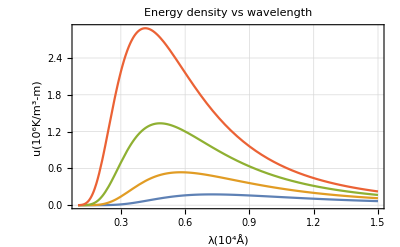

```mathematica
Plot[
Evaluate@
Table[ρ[λ,𝒯],{𝒯,Range[4,7]*1000}],{λ,0.1,1.5},
Frame->True,PlotRange->All,GridLines->Automatic,
PlotLabel->Style["Energy density vs wavelength",16],
FrameLabel->st@{"λ(10^4Å)","u(10^6K/m^3-m)"}
]
```

### Wien' s Displacement Law

```mathematica
dudλ=D[u[λ,𝒯],λ]
```

(8 c^2 ⅇ^((c h)/(k_B 𝒯 λ)) h^2 π)/((-1+ⅇ^((c h)/(k_B 𝒯 λ)))^2 k_B 𝒯 λ^7)-(40 c h π)/((-1+ⅇ^((c h)/(k_B 𝒯 λ))) λ^6)

```mathematica
num=Numerator[dudλ//Together]
```

-8 c h π (-c ⅇ^((c h)/(k_B 𝒯 λ)) h-5 k_B 𝒯 λ+5 ⅇ^((c h)/(k_B 𝒯 λ)) k_B 𝒯 λ)

```mathematica
num/.λ->((c h)/ (Subscript[k, b] x))/𝒯//Simplify
```

(8 c^2 h^2 π (-5 (-1+ⅇ^((x k_b)/k_B)) k_B+ⅇ^((x k_b)/k_B) x k_b))/(x k_b)

```mathematica
eq=5+ⅇ^x(x-5);
```

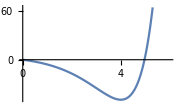

```mathematica
Plot[eq,{x,0,6},ImageSize->Small]
```

```mathematica
sol=FindRoot[eq,{x,5}]
```

{x→4.96511}

```mathematica
Subscript[λ, max]=((c h)/ (Subscript[k, B] x))/𝒯/.sol[[1]]
```

(0.201405 c h)/(k_B 𝒯)

### λ_max for Solar Radiation

```mathematica
Subscript[λ, max]/.constantValues/.𝒯->Quantity[5772., "Kelvins"]
```

0.0000348935 h c/(K k)

```mathematica
UnitConvert[%,"Angstroms"]
```

5020.39 Å

## Particle in an Infinite Box

Wave function, infinite superposition

Ψ (x, t) =∑_(n=1)^∞ [c_n^+ϕ_n^+(x)ⅇ^(-ⅈE_n^+t)+c_n^-ϕ_n^-(x) ⅇ^(-ⅈE_n^-t)]

where:

c_n^±=∫_-a^a ϕ_n^±(x)Ψ(x,0)ⅆx

initial Gaussian wave packet:

Ψ(x,0)=(1/(2 πL^2))^(1/4)ⅇ^(ⅈk_0 x)ⅇ^(-x^2/4 L^2)

Numerical-Symbolic solution

```mathematica
particleInABoxProbabilityDensity[x,0]//Short[#,20]&
```

0.+0.00512242 Cos[14.1372 x]^2+0.0391871 Cos[14.1372 x] Cos[17.2788 x]+0.0749466 Cos[17.2788 x]^2+0.0558815 Cos[14.1372 x] Cos[20.4204 x]+0.21375 Cos[17.2788 x] Cos[20.4204 x]+0.152406 Cos[20.4204 x]^2+0.0301726 Cos[14.1372 x] Cos[23.5619 x]+0.115412 Cos[17.2788 x] Cos[23.5619 x]+0.16458 Cos[20.4204 x] Cos[23.5619 x]+0.0444315 Cos[23.5619 x]^2+0.00607787 Cos[14.1372 x] Cos[26.7035 x]+0.0232482 Cos[17.2788 x] Cos[26.7035 x]+0.0331524 Cos[20.4204 x] Cos[26.7035 x]+0.0179003 Cos[23.5619 x] Cos[26.7035 x]+0.00180288 Cos[26.7035 x]^2+«5»+0.136126 Sin[18.8496 x]^2+0.0165789 Sin[12.5664 x] Sin[21.9911 x]+0.102945 Sin[15.708 x] Sin[21.9911 x]+0.239425 Sin[18.8496 x] Sin[21.9911 x]+0.105278 Sin[21.9911 x]^2+0.00544505 Sin[12.5664 x] Sin[25.1327 x]+0.0338105 Sin[15.708 x] Sin[25.1327 x]+0.0786348 Sin[18.8496 x] Sin[25.1327 x]+0.0691533 Sin[21.9911 x] Sin[25.1327 x]+0.0113561 Sin[25.1327 x]^2+0.000707558 Sin[12.5664 x] Sin[28.2743 x]+0.00439351 Sin[15.708 x] Sin[28.2743 x]+0.0102182 Sin[18.8496 x] Sin[28.2743 x]+0.00898613 Sin[21.9911 x] Sin[28.2743 x]+0.00295134 Sin[25.1327 x] Sin[28.2743 x]+0.000191756 Sin[28.2743 x]^2

```mathematica
NIntegrate[particleInABoxProbabilityDensity[x,0],{x,-1,1}]
```

0.557479

```mathematica
particleInABoxProbabilityDensity[x,t]//Short[#,20]&
```

0.00512242 Cos[99.9297 t]^2 Cos[14.1372 x]^2+0.0391871 Cos[99.9297 t] Cos[149.278 t] Cos[14.1372 x] Cos[17.2788 x]+0.0749466 Cos[149.278 t]^2 Cos[17.2788 x]^2+0.0558815 Cos[99.9297 t] Cos[208.495 t] Cos[14.1372 x] Cos[20.4204 x]+0.21375 Cos[149.278 t] Cos[208.495 t] Cos[17.2788 x] Cos[20.4204 x]+0.152406 Cos[208.495 t]^2 Cos[20.4204 x]^2+0.0301726 Cos[99.9297 t] Cos[277.583 t] Cos[14.1372 x] Cos[23.5619 x]+0.115412 Cos[149.278 t] Cos[277.583 t] Cos[17.2788 x] Cos[23.5619 x]+0.16458 Cos[208.495 t] Cos[277.583 t] Cos[20.4204 x] Cos[23.5619 x]+«144»+0.00439351 Sin[123.37 t] Sin[399.719 t] Sin[15.708 x] Sin[28.2743 x]+0.0102182 Cos[177.653 t] Cos[399.719 t] Sin[18.8496 x] Sin[28.2743 x]+0.0102182 Sin[177.653 t] Sin[399.719 t] Sin[18.8496 x] Sin[28.2743 x]+0.00898613 Cos[241.805 t] Cos[399.719 t] Sin[21.9911 x] Sin[28.2743 x]+0.00898613 Sin[241.805 t] Sin[399.719 t] Sin[21.9911 x] Sin[28.2743 x]+0.00295134 Cos[315.827 t] Cos[399.719 t] Sin[25.1327 x] Sin[28.2743 x]+0.00295134 Sin[315.827 t] Sin[399.719 t] Sin[25.1327 x] Sin[28.2743 x]+0.000191756 Cos[399.719 t]^2 Sin[28.2743 x]^2+0.000191756 Sin[399.719 t]^2 Sin[28.2743 x]^2

Animation

```mathematica
frames=336;
δt=(16/π)/frames//N
```

0.0151576

```mathematica
pDensPlots=Table[
(*Evaluates improve performance*)
Plot[Evaluate[particleInABoxProbabilityDensity[x,t]],
{x,-1,1},PlotRange->{0,2.5}]
,
{t,0,16}
];
```

```mathematica
ListAnimate[pDensPlots]
```